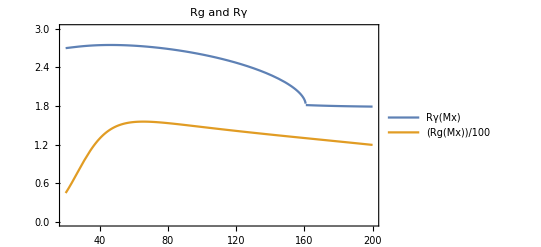

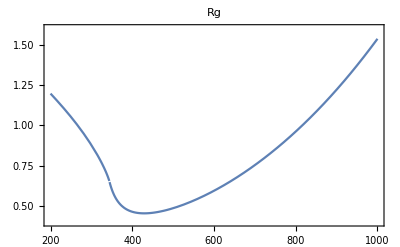

LogLogPlot::prng: Value of option PlotRange -> {{100\ PlotLegends, 1000\ PlotLegends}, {PlotLegends, 150\ PlotLegends}} → "Expressions" is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

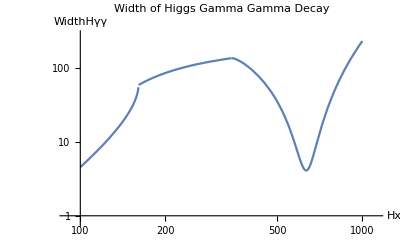

-Graphics3D-

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

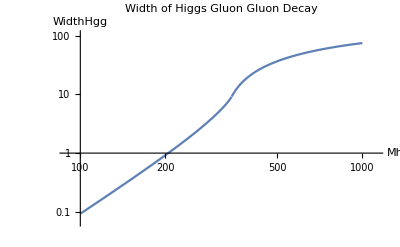

-Graphics3D-

-Graphics3D-

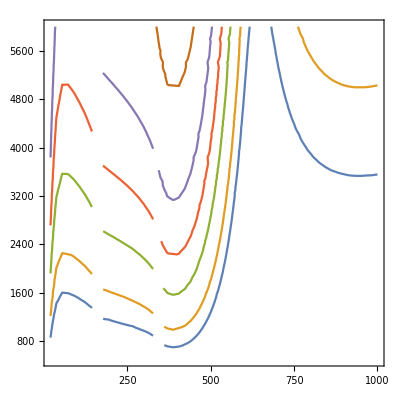

```mathematica
Me=.0000511;
Mμ=.1057;
Mτ=1.777;
MW=80.4;
Mu= 0.0023;
Md= 0.0048;
Ms = 0.095;
Mc = 1.4;
Mt = 172;
Mb  = 4.2;
v=246;
Bem[Mx_]=-11/3;
Bg[Mx_]=7;
taue[Mx_]=4*(Me^2)/(Mx^2);
tauμ[Mx_]=4*(Mμ^2)/(Mx^2);
tauτ[Mx_]=4*(Mτ^2)/(Mx^2);
tauW[Mx_]=4*(MW^2)/(Mx^2);
tauu[Mx_]=4*(Mu^2/(Mx)^2);
taud[Mx_]=4*(Md^2/(Mx)^2);
taus[Mx_]=4*(Ms^2/(Mx)^2);
tauc[Mx_]=4*(Mc^2/(Mx)^2);
taut[Mx_]=4*(Mt^2/(Mx)^2);
taub[Mx_] = 4*(Mb^2/(Mx)^2);
ft[taui_]=Piecewise[{{(ArcSin[Sqrt[1/taui]])^2,taui≥1},{(-1/4)*(Log[(1+Sqrt[1-taui])/(1-Sqrt[1-taui])]-ⅈ*π)^2,taui<1}}];
F1[tau1_]=2+3*tau1+(3*tau1)*(2-tau1)*ft[tau1];
F12[tau12_]= -2*tau12*(1+(1-tau12)*ft[tau12]);
SumLoopCorrectionRγ[Mx_]=       F12[taue[Mx]]+F12[tauμ[Mx]]+F12[tauτ[Mx]]+F1[tauW[Mx]] + 3*(2/3)^2*F12[tauu[Mx]]+3*(-1/3)^2*F12[taud[Mx]]+ 3*(2/3)^2*F12[tauc[Mx]]+3*(-1/3)^2*F12[taus[Mx]]+ 3*(2/3)^2*F12[taut[Mx]]+3*(-1/3)^2*F12[taub[Mx]];
SumLoopCorrectionRg[Mx_]=F12[tauu[Mx]]+F12[taud[Mx]]+F12[taus[Mx]]+F12[tauc[Mx]]+F12[taut[Mx]]+F12[taub[Mx]];
Rg[Mx_]=(Abs[-Bg[Mx]+(1/2)*SumLoopCorrectionRg[Mx]])^2/(Abs[(1/2)*SumLoopCorrectionRg[Mx]])^2;
Rγ[Mx_]=(Abs[-Bem[Mx]+SumLoopCorrectionRγ[Mx]])^2/(Abs[SumLoopCorrectionRγ[Mx]])^2;
Plot[{Rγ[Mx],Rg[Mx]/100},{Mx,20,200},PlotRange ->{{20,200},{0,3}},PlotLegends->"Expressions",Frame->True, AxesOrigin->{20,0},PlotLabel->"Rg and Rγ"]
Plot[Rg[Mx]/100,{Mx,200,1000},PlotRange ->{{200,1000},{.4,1.6}},PlotLegends->"Expressions",Frame->True, AxesOrigin->{20,0},PlotLabel ->"Rg"]
(*Higgs Width Function peices end with H*)
Gμ=1.16637*10^-5;
α=1/128;
αs = .1172;
taueH[Mh_]=Mh^2/(4*(Me)^2);
tauμH[Mh_]=Mh^2/(4*(Mμ)^2);
tauτH[Mh_]=Mh^2/(4*(Mτ)^2);
tauWH[Mh_]=Mh^2/(4*(MW)^2);
tauuH[Mh_]=Mh^2/(4*(Mu)^2);
taudH[Mh_]=Mh^2/(4*(Md)^2);
tausH[Mh_]=Mh^2/(4*(Ms)^2);
taucH[Mh_]=Mh^2/(4*(Mc)^2);
tautH[Mh_]=Mh^2/(4*(Mt)^2);
taubH[Mh_]=Mh^2/(4*(Mb)^2);
(*f(t) for the Higgs*)
ftH[tauHi_]= Piecewise[{{(ArcSin[Sqrt[tauHi]]^2),tauHi ≤ 1},{(-1/4)*(Log[(1+Sqrt[1-(tauHi)^-1])/(1-Sqrt[1-(tauHi)^-1])]-ⅈ*π)^2,tauHi > 1}}];
(*Form Factors for spim 1/2 and spin 1 particles*)
A12H[tauHi_]=2(tauHi+(tauHi-1)*ftH[tauHi])*(tauHi)^-2;
A1H[tauHi_]=-(2*(tauHi)^2+3*tauHi+3(2*tauHi-1)*ftH[tauHi])*tauHi^-2;
SumFermionsAndWHiggs[Mh_]=A12H[taueH[Mh]]+A12H[tauμH[Mh]]+A12H[tauτH[Mh]]+A1H[tauWH[Mh]] + 3*(2/3)^2*A12H[tauuH[Mh]]+3*(-1/3)^2*A12H[taudH[Mh]]+ 3*(2/3)^2*A12H[taucH[Mh]]+3*(-1/3)^2*A12H[tausH[Mh]]+ 3*(2/3)^2*A12H[tautH[Mh]]+3*(-1/3)^2*A12H[taubH[Mh]];
(*Width is in GeV*)
WidthHγγ[Mh_]=((Gμ*α^2*(Mh)^3)/(128*Sqrt[2]*π^3))*(Abs[SumFermionsAndWHiggs[Mh]])^2;
(*Plot is in KeV to match the paper*)
LogLogPlot[Re[WidthHγγ[Mh]]*1000000,{Mh,100,1000},PlotRange ->{{100,1000},{1,150}}PlotLegends->"Expressions",AxesLabel -> {Hx,WidthHγγ},AxesOrigin->{100,0},PlotLabel ->"Width of Higgs Gamma Gamma Decay"]
(*Now here is the width of the Dilaton Gamma Gamma Decay*)
WidthXγγ[Mx_,f_]=Rγ[Mx]*(v^2/f^2)* WidthHγγ[Mx];
Plot3D[WidthXγγ[Mx,f],{f,500,3000},{Mx,0,1000}, ColorFunction->"TemperatureMap",PlotLabel-> "Width of the Dilaton Gamma Gamma Decay",AxesLabel->{"f(GeV)","Mx (GeV)","Γ(X->γγ)(GeV)"}]
(*This is the Higgs -> gg width Note:Graph is in MeV and function is in GeV*)
SumQuarks[Mh_]=A12H[taubH[Mh]]+A12H[tautH[Mh]];
WidthHgg[Mh_]= ((Gμ*αs^2*Mh^3)/(36*Sqrt[2]*π^3))*(Abs[(3/4)* SumQuarks[Mh]])^2;
LogLogPlot[WidthHgg[Mh]*1000,{Mh,100,1000},PlotLegends->"Expressions",AxesLabel -> {Mh,WidthHgg},AxesOrigin->{100,0},PlotLabel ->"Width of Higgs Gluon Gluon Decay"]
(*Now here is the width of the Dilaton gluon gluon Decay*)
WidthXgg[Mx_,f_]= Rg[Mx]*(v^2/f^2)* WidthHgg[Mx];
Plot3D[WidthXgg[Mx,f],{f,500,3000},{Mx,0,1000}, ColorFunction->"TemperatureMap",PlotLabel-> "Width of the Dilaton Gluon Gluon Decay",AxesLabel->{"f(GeV)","Mx(GeV)","Γ(X->γγ)(GeV)"}]
(* This would be a way to check our contours from paper 7 I dont think this is right*)
σggXγγOVERσggHγγ[f_,Mx_]=Rg[Mx]*((v^2)/(f^2))*Rγ[Mx];
Plot3D[σggXγγOVERσggHγγ[f,Mx],{Mx,20,200},{f,500,4500}]
ContourPlot[{σggXγγOVERσggHγγ[f,Mx]== 10,σggXγγOVERσggHγγ[f,Mx]== 5,σggXγγOVERσggHγγ[f,Mx]== 2,σggXγγOVERσggHγγ[f,Mx]== 1,σggXγγOVERσggHγγ[f,Mx]== .5,σggXγγOVERσggHγγ[f,Mx]== .2,σggXγγOVERσggHγγ[f,Mx]== .1},{Mx,20,1000},{f,500,6000}]
```